```mathematica
Off[General::munfl]
SetDirectory[NotebookDirectory[]]
```

/home/kirscher/kette_repo/AcoreNteraction/source_mathematica

```mathematica
lecs={{0.25,0.0036,-30.9795},{1.00,0.0036,-117.5248},{2.25,0.0036,-259.7207},{4.00,0.0036,-457.5555},{6.25,0.0036,-711.0607},{9.00,0.0036,-1020.1831},{12.25,0.0036,-1385.0069},{16.00,0.0036,-1805.4404},{20.25,0.0036,-2281.5596},{25.00,0.0036,-2813.2897}};
lecnbr=Length[lecs];
corescale=4;
Rmax=80;nGrid=1250;
RmaxFF=20;nGridFF=5000;
```

## Finite differences

```mathematica
SolveSecularL0[ Rdis_?NumberQ,Npoints_?NumberQ,mh2_?NumberQ,V0_,W_,α_,λ_,C0_]:=Block[{e,Rmax,nGrid,hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,asywf,wf,wffree,Tere,fit,nn,δ,L,r,mod,usol},
Rmax=Rdis;
nGrid=Npoints;
hDif=Rmax/nGrid;
L=0;

(* Matrix components *)
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{nGrid,nGrid}];
Dmat=DiagonalMatrix[Table[hDif^2 mh2(-V0[i hDif,α,λ,C0])+(L(L+1))/i^2,{i,1,nGrid}]];

(*Print[">> ... Local approximation ..."];*)
Wmat=DiagonalMatrix[Table[hDif^2 mh2 W[i hDif,i hDif,0.0,α,λ,C0],{i,1,nGrid}]];

bcol=Table[Which[i==nGrid,-hDif,1==1,0],{i,1,nGrid}];
Dmat⟦nGrid⟧⟦nGrid⟧+=1; (*this is only for 0 energy*)

ucol=Array[Subscript["u", ##]&,{nGrid}];
Amat=Dmat+Wmat+Kmat;

usol=LinearSolve[Amat,bcol];
wf=Table[{i hDif,usol⟦i⟧},{i,1,nGrid}];

wffree=Table[{i hDif,(usol[[-1]]-usol[[-2]]) i+usol[[-2]]-(usol[[-1]]-usol[[-2]]) nGrid},{i,1,nGrid}];
Tere=Rmax-usol⟦-1⟧;

{Tere,wffree,wf}
]
```

```mathematica
SolveSecularLnz[Ene_?NumberQ, Rdis_?NumberQ,Npoints_?NumberQ,mh2_?NumberQ,V0_,W_,α_,λ_,C0_]:=Block[{e,Rmax,nGrid,hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,asywf,wf,wffree,Tere,fit,nn,δ,L,r,mod,usol},
e=Ene;
Rmax=Rdis;
nGrid=Npoints;
hDif=Rmax/nGrid;
L=0;

(* Matrix components *)
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{nGrid,nGrid}];
Dmat=DiagonalMatrix[Table[hDif^2 mh2(e-V0[i hDif,α,λ,C0])+(L(L+1))/i^2,{i,1,nGrid}]];
(*Print[">> ... Local approximation ..."];*)
Wmat=DiagonalMatrix[Table[hDif^2 mh2 W[i hDif,i hDif, e,α,λ,C0],{i,1,nGrid}]];

bcol=Table[Which[i==nGrid,-1,1==1,0],{i,1,nGrid}];

ucol=Array[Subscript["u", ##]&,{nGrid}];
Amat=Dmat+Wmat+Kmat;

usol=LinearSolve[Amat,bcol];
wf=Table[{i hDif,usol⟦i⟧},{i,1,nGrid}];

asywf=nn Sin[Sqrt[mh2 e] r+δ];
fit=FindFit[wf,asywf,{nn,δ},r];
mod=Function[{r},Evaluate[asywf/.fit]];wffree=Table[{i hDif,mod[i hDif]},{i,1,nGrid}];
Tere=-(1/Sqrt[mh2 e]) Tan[δ/.fit[[2]]];

{Tere,wffree,wf}
]
```

```mathematica
SolveSecularNL0[Rdis_?NumberQ,Npoints_?NumberQ,mh2_?NumberQ,V0_,W_,α_,λ_,C0_]:=Block[{e,Rmax,nGrid,hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,asywf,wf,wffree,Tere,fit,nn,δ,L,r,mod,usol},
e=0.0;
Rmax=Rdis;
nGrid=Npoints;
hDif=Rmax/nGrid;
L=0;

(* Matrix components *)
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{nGrid,nGrid}];
Dmat=DiagonalMatrix[Table[hDif^2 mh2(e-V0[i hDif,α,λ,C0])+(L(L+1))/i^2,{i,1,nGrid}]];
Wmat=Table[hDif^2 mh2 W[i hDif,j hDif, e,α,λ,C0],{i,1,nGrid},{j,1,nGrid}]; 

bcol=Table[Which[i==nGrid,-hDif,1==1,0],{i,1,nGrid}];
Dmat⟦nGrid⟧⟦nGrid⟧+=1; (*this is only for 0 energy*)

ucol=Array[Subscript["u", ##]&,{nGrid}];
Amat=Dmat+Wmat+Kmat;

usol=LinearSolve[Amat,bcol];
wf=Table[{i hDif,usol⟦i⟧},{i,1,nGrid}];

wffree=Table[{i hDif,(usol[[-1]]-usol[[-2]]) i+usol[[-2]]-(usol[[-1]]-usol[[-2]]) nGrid},{i,1,nGrid}];
Tere=Rmax-usol⟦-1⟧;

{Tere,wffree,wf}
]
```

```mathematica
SolveSecularNLnz[Ene_?NumberQ, Rdis_?NumberQ,Npoints_?NumberQ,mh2_?NumberQ,V0_,W_,α_,λ_,C0_]:=Block[{e,Rmax,nGrid,hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,asywf,wf,wffree,Tere,fit,nn,δ,L,r,mod,usol},
e=Ene;
Rmax=Rdis;
nGrid=Npoints;
hDif=Rmax/nGrid;
L=0;

(* Matrix components *)
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{nGrid,nGrid}];
Dmat=DiagonalMatrix[Table[hDif^2 mh2(e-V0[i hDif,α,λ,C0])+(L(L+1))/i^2,{i,1,nGrid}]];

Wmat=Table[hDif^2 mh2 W[i hDif,j hDif, e,α,λ,C0],{i,1,nGrid},{j,1,nGrid}]; 

bcol=Table[Which[i==nGrid,-1,1==1,0],{i,1,nGrid}];

ucol=Array[Subscript["u", ##]&,{nGrid}];
Amat=Dmat+Wmat+Kmat;

usol=LinearSolve[Amat,bcol];
wf=Table[{i hDif,usol⟦i⟧},{i,1,nGrid}];
asywf=nn Sin[Sqrt[mh2 e] r+δ];
fit=FindFit[wf,asywf,{nn,δ},r];
mod=Function[{r},Evaluate[asywf/.fit]];wffree=Table[{i hDif,mod[i hDif]},{i,1,nGrid}];
Tere=-(1/Sqrt[mh2 e]) Tan[δ/.fit[[2]]];

{Tere,wffree,wf}
]
```

### nucleon-nucleon EFT_nopi leading-order benchmark

μ = 469.46 MeV    hbarc = 197.327 MeV·fm    h^2/2μ = 41.471 MeV·fm^2

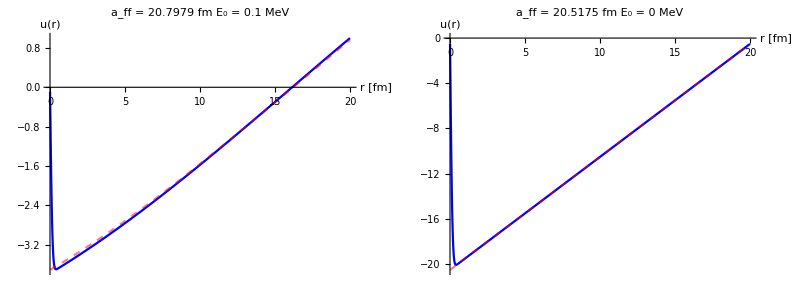

```mathematica
μ=938.92/2;hbar=197.327053;mh2=(2 μ)/(hbar)^2;e1=0.1;α=0;
Print["μ = ", μ, " MeV    hbarc = ",hbar, " MeV·fm    h^2/2μ = ", N[1/mh2 ]," MeV·fm^2"];

Λ=lecs[[lecnbr]][[1]];λ=Λ;
C0=lecs[[lecnbr]][[3]];
V0[r_,α_,λ_,C0_]:= C0 Exp[- λ r^2];
W[r_,rp_,e_,α_,λ_,C0_]:=0;

nonzeroSOL=SolveSecularLnz[e1,RmaxFF,nGridFF,mh2,V0,W,α,λ,C0];
zeroSOL=SolveSecularL0[RmaxFF,nGridFF,mh2,V0,W,α,λ,C0];

Grid[{{
ListLinePlot[{nonzeroSOL[[3]],nonzeroSOL[[2]]},PlotStyle->{Blue,{Red,Opacity->0.5,Dashed}},AxesLabel->{"r [fm]","u(r)"},PlotRange->{Automatic,Automatic},PlotLabel->"a_ff = "<>ToString[nonzeroSOL[[1]]]<>" fm    E_0 = "<>ToString[e1]<>" MeV",ImageSize->Large],
ListLinePlot[{zeroSOL[[3]],zeroSOL[[2]]},PlotStyle->{Blue,{Red,Opacity->0.5,Dashed}},AxesLabel->{"r [fm]","u(r)"},PlotRange->{Automatic,Automatic},PlotLabel->"a_ff = "<>ToString[zeroSOL[[1]]]<>" fm    E_0 = 0 MeV",ImageSize->Large]}}]
```

λ =   0.25 fm^-2     C_0 =     -30.9795 MeV     a_0 =  21.84 fm

λ =   1.00 fm^-2     C_0 =    -117.5248 MeV     a_0 =  21.10 fm

λ =   2.25 fm^-2     C_0 =    -259.7207 MeV     a_0 =  20.85 fm

λ =   4.00 fm^-2     C_0 =    -457.5555 MeV     a_0 =  20.76 fm

λ =   6.25 fm^-2     C_0 =    -711.0607 MeV     a_0 =  20.67 fm

λ =   9.00 fm^-2     C_0 =   -1020.1831 MeV     a_0 =  20.65 fm

λ =  12.25 fm^-2     C_0 =   -1385.0069 MeV     a_0 =  20.59 fm

λ =  16.00 fm^-2     C_0 =   -1805.4404 MeV     a_0 =  20.57 fm

λ =  20.25 fm^-2     C_0 =   -2281.5596 MeV     a_0 =  20.53 fm

λ =  25.00 fm^-2     C_0 =   -2813.2897 MeV     a_0 =  20.52 fm

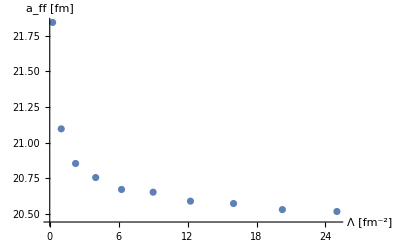

```mathematica
affofL={};
μ=938.92/2;hbar=197.327053;mh2=(μ 2)/(hbar)^2;
Do[
Λ=pot[[1]];λ=Λ;
C0=pot[[3]];
V0[r_,α_,λ_,C0_]:= C0 Exp[- λ r^2];
W[r_,rp_,e_,α_,λ_,C0_]:=0;

a0=SolveSecularL0[RmaxFF,nGridFF,mh2,V0,W,α,λ,C0][[1]];
AppendTo[affofL,{Λ,a0}];

Print["λ = ",NumberForm[λ,{4,2},NumberPadding->{" ","0"}]," fm^-2     C_0 = ",NumberForm[C0,{10,4},NumberPadding->{" ","0"}]," MeV     a_0 = ",NumberForm[a0,{4,2},NumberPadding->{" ","0"}]," fm"]
,{pot,lecs}]
ListPlot[affofL,AxesLabel->{"Λ [fm^-2]","a_ff [fm]"}]
```

### (AB)-(AB) dimer-dimer EFT_nopi leading-order calculation

single-channel RGM in zero-energy, zero-range, and local-approximation

μ = 938.92     hbarc = 197.327     h^2/2μ = 20.7355

λ = 25.fm^-2     C_0 = -2813.29MeV    α = 0.0144fm^-2

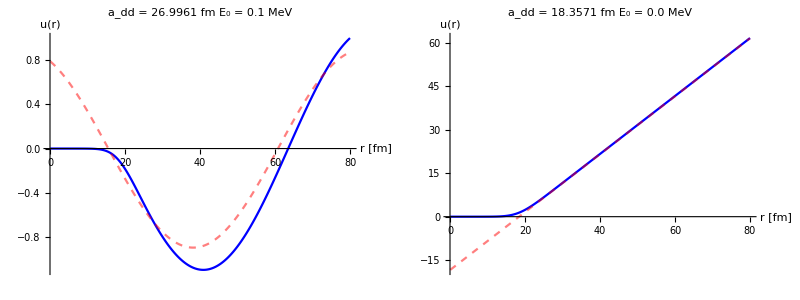

```mathematica
μ=938.92;mh2=(2 μ)/(hbar)^2;hbar=197.327053;e1=0.1;

Λ=lecs[[lecnbr]][[1]];λ=Λ;
α=corescale lecs[[lecnbr]][[2]];
C0=lecs[[lecnbr]][[3]];
Print["μ = ", μ, "     hbarc = ",hbar, "     h^2/2μ = ", N[1/mh2 ]];
Print["λ = ",λ,"fm^-2     C_0 = ",C0,"MeV    α = ",α,"fm^-2"];
(* eq.(23) OverHat[=] zero-range, zero-energy, and localized (ab)-(ab) potential *)
V0[r_,α_,λ_,C0_]:=hbar^2/(2 μ) (4 α^2 r^2-2 α) 8 Pi^1.5 Exp[-α r^2]+C0 (2 α/(2 α+λ))^1.5 (2 Exp[-2 α r^2]-16 Pi^1.5 Exp[-3 α r^2]);
W[r_,rp_,e_,α_,λ_,C0_]:=0;

nonzeroSOL=SolveSecularLnz[e1,Rmax,nGrid,mh2,V0,W,α,λ,C0];
zeroSOL=SolveSecularL0[Rmax,nGrid,mh2,V0,W,α,λ,C0];

Grid[{{
ListLinePlot[{nonzeroSOL[[3]],nonzeroSOL[[2]]},PlotStyle->{Blue,{Red,Opacity->0.5,Dashed}},AxesLabel->{"r [fm]","u(r)"},PlotRange->{Automatic,Automatic},PlotLabel->"a_dd = "<>ToString[nonzeroSOL[[1]]]<>" fm    E_0 = "<>ToString[e1]<>" MeV",ImageSize->Large],
ListLinePlot[{zeroSOL[[3]],zeroSOL[[2]]},PlotStyle->{Blue,{Red,Opacity->0.5,Dashed}},AxesLabel->{"r [fm]","u(r)"},PlotRange->{Automatic,Automatic},PlotLabel->"a_dd = "<>ToString[zeroSOL[[1]]]<>" fm    E_0 = 0.0 MeV",ImageSize->Large]}}]
```

λ =   0.25 fm^-2     C_0 =     -30.9795 MeV     a_0 =  18.36 fm

λ =   1.00 fm^-2     C_0 =    -117.5248 MeV     a_0 =  18.36 fm

λ =   2.25 fm^-2     C_0 =    -259.7207 MeV     a_0 =  18.36 fm

λ =   4.00 fm^-2     C_0 =    -457.5555 MeV     a_0 =  18.36 fm

λ =   6.25 fm^-2     C_0 =    -711.0607 MeV     a_0 =  18.36 fm

λ =   9.00 fm^-2     C_0 =   -1020.1831 MeV     a_0 =  18.36 fm

λ =  12.25 fm^-2     C_0 =   -1385.0069 MeV     a_0 =  18.36 fm

λ =  16.00 fm^-2     C_0 =   -1805.4404 MeV     a_0 =  18.36 fm

λ =  20.25 fm^-2     C_0 =   -2281.5596 MeV     a_0 =  18.36 fm

λ =  25.00 fm^-2     C_0 =   -2813.2897 MeV     a_0 =  18.36 fm

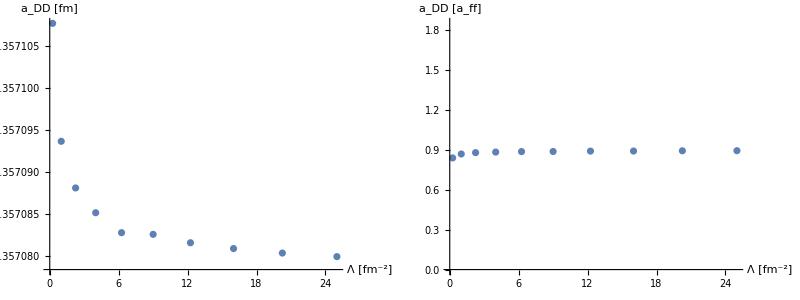

```mathematica
addofL={};μ=938.92;mh2=(2 μ)/(hbar)^2;hbar=197.327053;
Do[
Λ=pot[[1]];λ=Λ;
C0=pot[[3]];α=corescale pot[[2]];
V0[r_,α_,λ_,C0_]:=1/mh2 (4 α^2 r^2-2 α) 8 Pi^1.5 Exp[-α r^2]+C0 (2 α/(2 α+λ))^1.5 (2 Exp[-2 α r^2]-16 Pi^1.5 Exp[-3 α r^2]);
W[r_,rp_,e_,α_,λ_,C0_]:=0;

a0=SolveSecularL0[Rmax,nGrid,mh2,V0,W,α,λ,C0][[1]];
AppendTo[addofL,{Λ,a0}];

Print["λ = ",NumberForm[λ,{4,2},NumberPadding->{" ","0"}]," fm^-2     C_0 = ",NumberForm[C0,{10,4},NumberPadding->{" ","0"}]," MeV     a_0 = ",NumberForm[a0,{4,2},NumberPadding->{" ","0"}]," fm"]
,{pot,lecs}]
addbyaffofL=Table[{lecs[[n]][[1]],addofL[[n]][[2]]/affofL[[n]][[2]]},{n,Length[lecs]}];
Grid[{{ListPlot[addofL,AxesLabel->{"Λ [fm^-2]","a_DD [fm]"}],ListPlot[addbyaffofL,PlotRange->{Automatic,{0,2.1 Mean[addbyaffofL[[All,2]]]}},AxesLabel->{"Λ [fm^-2]","a_DD [a_ff]"}]}}]
```

single-channel RGM (non-local)

μ = 938.92     hbarc = 197.327     h^2/2μ = 20.7355

λ = 25.fm^-2     C_0 = -2813.29MeV    α = 0.0144fm^-2

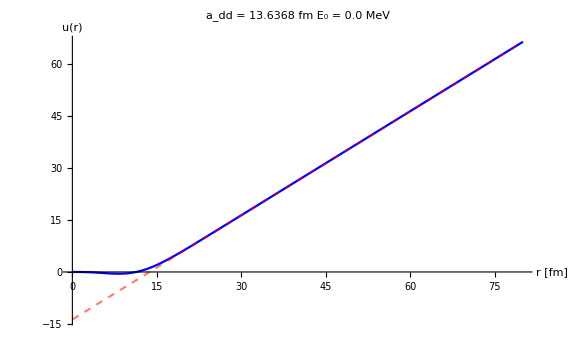

```mathematica
lecnbr=10;
μ=938.92;mh2=(2 μ)/(hbar)^2;hbar=197.327053;

Λ=lecs[[lecnbr]][[1]];λ=Λ;
α=corescale lecs[[lecnbr]][[2]];
C0=lecs[[lecnbr]][[3]];
Print["μ = ", μ, "     hbarc = ",hbar, "     h^2/2μ = ", N[1/mh2 ]];
Print["λ = ",λ,"fm^-2     C_0 = ",C0,"MeV    α = ",α,"fm^-2"];
(* eq.(21) *)
V0[r_,α_,λ_,C0_]:=C0 (2 α/(2 α+λ))^1.5 Exp[-2 α λ/(2 α+λ) r^2];
(* eq.(22) with partial-wave-projection coefficients *)
W[r_,rp_,e_,α_,λ_,C0_]:=(4π r rp) 8 α^(3/2) (mh2^(-1) ((4 α^2 r^2-2 α)+e)ⅇ^(-α(rp^2+r^2))-2 C0(2 α/(2 α+λ))^1.5 ⅇ^(-α(rp^2+(2α+3λ)/(2α+λ)r^2)));

zeroSOL=SolveSecularNL0[Rmax,nGrid,mh2,V0,W,α,λ,C0];

ListLinePlot[{zeroSOL[[3]],zeroSOL[[2]]},PlotStyle->{Blue,{Red,Opacity->0.5,Dashed}},AxesLabel->{"r [fm]","u(r)"},PlotRange->{Automatic,Automatic},PlotLabel->"a_dd = "<>ToString[zeroSOL[[1]]]<>" fm    E_0 = 0.0 MeV",ImageSize->Large]
```

μ = 938.92     hbarc = 197.327     h^2/2μ = 20.7355

λ = 25.fm^-2     C_0 = -2813.29MeV    α = 0.0144fm^-2

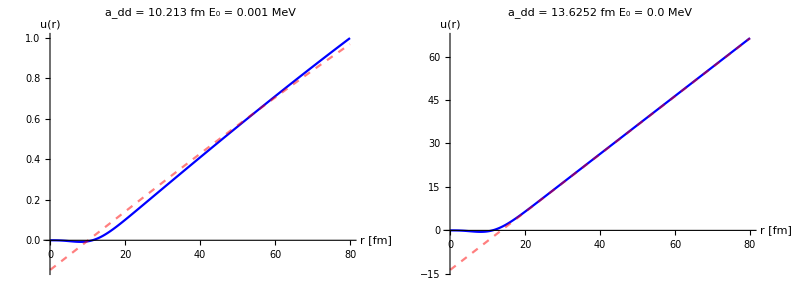

```mathematica
lecnbr=10;
μ=938.92;mh2=(2 μ)/(hbar)^2;hbar=197.327053;e1=0.001;

Λ=lecs[[lecnbr]][[1]];λ=Λ;
α=corescale lecs[[lecnbr]][[2]];
C0=lecs[[lecnbr]][[3]];
Print["μ = ", μ, "     hbarc = ",hbar, "     h^2/2μ = ", N[1/mh2 ]];
Print["λ = ",λ,"fm^-2     C_0 = ",C0,"MeV    α = ",α,"fm^-2"];
(* eq.(21) *)
V0[r_,α_,λ_,C0_]:=2 C0 (2 α/(2 α+λ))^1.5 Exp[-2 α λ/(2 α+λ) r^2];
(* eq.(22) with partial-wave-projection coefficients *)
W[r_,rp_,e_,α_,λ_,C0_]:=(4π r rp) 8 α^(3/2) ((1/mh2 (4 α^2 r^2-2 α)+e) Exp[-α(rp^2+r^2)]-2 C0(2 α/(2 α+λ))^1.5 Exp[-α(rp^2+(2α+3λ)/(2α+λ)r^2)]);

nonzeroSOL=SolveSecularNLnz[e1,Rmax,nGrid,mh2,V0,W,α,λ,C0];
zeroSOL=SolveSecularNL0[Rmax,nGrid,mh2,V0,W,α,λ,C0];

Grid[{{
ListLinePlot[{nonzeroSOL[[3]],nonzeroSOL[[2]]},PlotStyle->{Blue,{Red,Opacity->0.5,Dashed}},AxesLabel->{"r [fm]","u(r)"},PlotRange->{Automatic,Automatic},PlotLabel->"a_dd = "<>ToString[nonzeroSOL[[1]]]<>" fm    E_0 = "<>ToString[e1]<>" MeV",ImageSize->Large],
ListLinePlot[{zeroSOL[[3]],zeroSOL[[2]]},PlotStyle->{Blue,{Red,Opacity->0.5,Dashed}},AxesLabel->{"r [fm]","u(r)"},PlotRange->{Automatic,Automatic},PlotLabel->"a_dd = "<>ToString[zeroSOL[[1]]]<>" fm    E_0 = 0.0 MeV",ImageSize->Large]}}]
```

λ =   0.25 fm^-2     C_0 =     -30.9795 MeV     a_DD =  11.17       a_ff =  21.84 fm       α =   0.014400 fm^-2

λ =   1.00 fm^-2     C_0 =    -117.5248 MeV     a_DD =  12.43       a_ff =  21.10 fm       α =   0.014400 fm^-2

λ =   2.25 fm^-2     C_0 =    -259.7207 MeV     a_DD =  12.91       a_ff =  20.85 fm       α =   0.014400 fm^-2

λ =   4.00 fm^-2     C_0 =    -457.5555 MeV     a_DD =  13.16       a_ff =  20.76 fm       α =   0.014400 fm^-2

λ =   6.25 fm^-2     C_0 =    -711.0607 MeV     a_DD =  13.31       a_ff =  20.67 fm       α =   0.014400 fm^-2

λ =   9.00 fm^-2     C_0 =   -1020.1831 MeV     a_DD =  13.42       a_ff =  20.65 fm       α =   0.014400 fm^-2

λ =  12.25 fm^-2     C_0 =   -1385.0069 MeV     a_DD =  13.49       a_ff =  20.59 fm       α =   0.014400 fm^-2

λ =  16.00 fm^-2     C_0 =   -1805.4404 MeV     a_DD =  13.55       a_ff =  20.57 fm       α =   0.014400 fm^-2

λ =  20.25 fm^-2     C_0 =   -2281.5596 MeV     a_DD =  13.59       a_ff =  20.53 fm       α =   0.014400 fm^-2

λ =  25.00 fm^-2     C_0 =   -2813.2897 MeV     a_DD =  13.63       a_ff =  20.52 fm       α =   0.014400 fm^-2

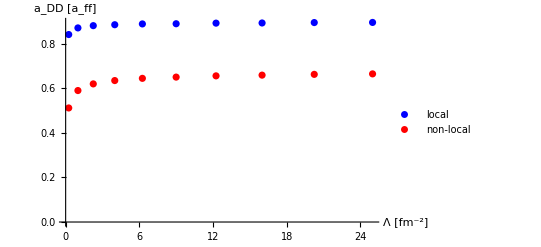

```mathematica
addofLNL={};μ=938.92;mh2=(2 μ)/(hbar)^2;hbar=197.327053;
iter=1;
Do[
Λ=pot[[1]];λ=Λ;
C0=pot[[3]];α=corescale pot[[2]];
(* eq.(21) *)
V0[r_,α_,λ_,C0_]:=2 C0 (2 α/(2 α+λ))^1.5 Exp[-2 α λ/(2 α+λ) r^2];
(* eq.(22) with partial-wave-projection coefficients *)
W[r_,rp_,e_,α_,λ_,C0_]:=(4π r rp) 8 α^(3/2) ((1/mh2 (4 α^2 r^2-2 α)+e) Exp[-α(rp^2+r^2)]-2 C0(2 α/(2 α+λ))^1.5 Exp[-α(rp^2+(2α+3λ)/(2α+λ)r^2)]);

a0=SolveSecularNL0[Rmax,nGrid,mh2,V0,W,α,λ,C0][[1]];
AppendTo[addofLNL,{Λ,a0}];
Print["λ = ",NumberForm[λ,{4,2},NumberPadding->{" ","0"}]," fm^-2     C_0 = ",NumberForm[C0,{10,4},NumberPadding->{" ","0"}]," MeV     a_DD = ",NumberForm[a0,{4,2},NumberPadding->{" ","0"}],"       a_ff = ",NumberForm[affofL[[iter]][[2]],{4,2},NumberPadding->{" ","0"}]," fm       α = ",NumberForm[α,{8,6},NumberPadding->{" ","0"}]," fm^-2"];iter=iter+1;
,{pot,lecs}]
addbyaffofLNL=Table[{lecs[[n]][[1]],addofLNL[[n]][[2]]/affofL[[n]][[2]]},{n,Length[lecs]}];
ListPlot[{addbyaffofL,addbyaffofLNL},PlotStyle->{Blue,{Red,Opacity->0.5,Dashed}},PlotLegends->{"local","non-local"},PlotRange->{Automatic,{0,Max[Max[addbyaffofL[[All,2]]],Max[addbyaffofLNL[[All,2]]]]}},AxesLabel->{"Λ [fm^-2]","a_DD [a_ff]"}]
```

```mathematica
Export["tmp.dat",addofLNL]
```

tmp.dat